```mathematica
Quiet@PacletUninstall["FernandoDuarte/LongRunRisk"]
```

```mathematica
PacletInstall[URL["https://github.com/GitHub-at-Brown/LongRunRisk/releases/download/pre-release-1.0.0/FernandoDuarte__LongRunRisk-1.0.0.paclet"],ForceVersionInstall->True]
```

```mathematica
Get["FernandoDuarte`LongRunRisk`"]
```

## Models available

```mathematica
Keys[Models]
```

{DES,NRCStochVol}

```mathematica
Info[Models]
```

```mathematica
m1 = Models["NRCStochVol"]; (*NRC+stochastic volatility of expected inflation*)
m2 = Models["DES"]; (*DES with long-run risk exposed to inflation*)
```

## NRC + stochastic volatility of expected inflation

### Yield Curve

```mathematica
meanYield=Simplify@UncondE[bondyield[t,m],m1]
meanNomYield=Simplify@UncondE[nombondyield[t,m],m1]
meanYieldCurve=Table[{m,100*meanYield},{m,1,120,6}];
meanNomYieldCurve=Table[{m,100*meanNomYield},{m,1,120,6}];
```

(-R[m][0]+Esp R[m][7])/m

(-P[m][0]+Esp P[m][7])/m

```mathematica
sol0 =m1["coeffsSolutionN"];
solP0= Union[m1["coeffsSolutionN"],m1["params"]];
```

```mathematica
Manipulate[
sol=Quiet[
ToNum["Rules",
m1,
{delta->deltaM,Esg->EsgM,Esp->EspM,gamma->gammaM,muc->mucM,mupbar->mupbarM,phic->phicM,phig->phigM,phip->phipM,phipbarpb->phipbarpbM,phispw->phispwM,psi->psiM,rhocp->rhocpM,rhog->rhogM,rhopbar->rhopbarM,rhoppbar->rhoppbarM,vp->vpM,xic->xicM,xip->xipM},
sol0,
 MaxIterations->500
]];
yc=ListLinePlot[meanYieldCurve//.sol,PlotLegends->{"Real"}, PlotStyle->{Orange,Thick},AxesLabel->{"Maturity in months","Yield"}];
nomyc=ListLinePlot[meanNomYieldCurve//.sol,PlotLegends->{"Nominal"}, PlotStyle->{Darker[Green],Thick}];
Show[yc,nomyc]
,
{{deltaM,0.99},0.9,0.99999},{{EsgM,-0.00624},-0.1,0.1},{{EspM,0.00111},0.00000001,0.1},{{gammaM,15},1.5,75},{{mucM,0.0016426},0.0,0.01},{{mupbarM,0.00327532},0.0,0.05},{{phicM,0.00204654},-0.01,0.1},{{phigM,0.002927236529485},-0.01,0.1},{{phipM,-0.0024624},-0.01,0.1},{{phipbarpbM,1.5},0,7.5},{{phispwM,1.81*^-7},1.0*^-12,1.0*^-5},{{psiM,2},0.5,5},{{rhocpM,-0.0521066},-1,1},{{rhogM,0.996289},0.01,0.9999},{{rhopbarM,0.9},0.01,0.99999},{{rhoppbarM,0.5},0,2.5},{{vpM,0.979},0.01,0.99999},{{xicM,-0.198287},-1,1},{{xipM,0.00073007},0.00000001,0.05},
UnsavedVariables->{sol,yc,nomyc},SynchronousInitialization->False,SynchronousUpdating->False,ContinuousAction->False
]
```

### Variance Ratios for Consumption

```mathematica
varianceRatio[horizon_,timeAggregation_,model_,var_:pi]:=UncondVar[Growth[var,t, "numPeriods"->horizon, "TimeAggregation"-> timeAggregation],model]/(horizon*UncondVar[Growth[var,t, "numPeriods"->1, "TimeAggregation"-> timeAggregation],model]);
```

```mathematica
vrdc=Table[{h-1,varianceRatio[h,1,m1,dc]},{h,1,60,6}];
```

```mathematica
vrdc//.sol0//.m1["params"]
```

{{0,1},{6,0.999153},{12,0.999614},{18,0.999974},{24,1.00024},{30,1.00043},{36,1.00058},{42,1.00069},{48,1.00078},{54,1.00085}}

```mathematica
Manipulate[
Quiet[sol=
ToNum["Rules",
m1,
{delta->deltaM,Esg->EsgM,Esp->EspM,gamma->gammaM,muc->mucM,mupbar->mupbarM,phic->phicM,phig->phigM,phip->phipM,phipbarpb->phipbarpbM,phispw->phispwM,psi->psiM,rhocp->rhocpM,rhog->rhogM,rhopbar->rhopbarM,rhoppbar->rhoppbarM,vp->vpM,xic->xicM,xip->xipM},
sol0,
 MaxIterations->500,
"initialGuess"-><|"Ewc"->{4.6}|>
];
];
vrh=ListLinePlot[vrdc//.sol,PlotLegends->{"Variance ratio"}, PlotStyle->{Orange,Thick},AxesLabel->{"Horizon","Ratio"}];
Show[vrh]
,
{{deltaM,0.99},0.9,0.99999},{{EsgM,-0.00624},-0.01,0.01},{{EspM,0.00111},0.00000001,0.1},{{gammaM,15},1.5,75},{{mucM,0.0016426},0.0,0.01},{{mupbarM,0.00327532},0.0,0.05},{{phicM,0.00204654},-0.01,0.1},{{phigM,0.002927236529485},-0.01,0.1},{{phipM,-0.0024624},-0.01,0.1},{{phipbarpbM,1.5},0,7.5},{{phispwM,1.81*^-7},1.0*^-12,1.0*^-5},{{psiM,2},0.5,5},{{rhocpM,-0.0521066},-1,1},{{rhogM,0.996289},0.01,0.9999},{{rhopbarM,0.9},0.01,0.99999},{{rhoppbarM,0.5},0,2.5},{{vpM,0.979},0.01,0.99999},{{xicM,-0.198287},-1,1},{{xipM,0.00073007},0.00000001,0.05},
UnsavedVariables->{sol,vrh},SynchronousInitialization->False,SynchronousUpdating->False,ContinuousAction->False
]
```

### Variance Ratios for Inflation

```mathematica
varianceRatio[horizon_,timeAggregation_,model_]:=UncondVar[Growth[pi,t, "numPeriods"->horizon, "TimeAggregation"-> timeAggregation],model]/(horizon*UncondVar[Growth[pi,t, "numPeriods"->1, "TimeAggregation"-> timeAggregation],model])
```

```mathematica
vr=Table[{h-1,varianceRatio[h,1,m1]},{h,1,60,6}];
```

```mathematica
vr//.sol0
```

{{0,1},{6,2.33169},{12,3.40831},{18,4.15919},{24,4.69273},{30,5.08105},{36,5.37073},{42,5.59205},{48,5.765},{54,5.90297}}

```mathematica
Manipulate[
Quiet[sol=
ToNum["Rules",
m1,
{delta->deltaM,Esg->EsgM,Esp->EspM,gamma->gammaM,muc->mucM,mupbar->mupbarM,phic->phicM,phig->phigM,phip->phipM,phipbarpb->phipbarpbM,phispw->phispwM,psi->psiM,rhocp->rhocpM,rhog->rhogM,rhopbar->rhopbarM,rhoppbar->rhoppbarM,vp->vpM,xic->xicM,xip->xipM},
sol0,
 MaxIterations->500,
"initialGuess"-><|"Ewc"->{4.6}|>
];
];
vrh=ListLinePlot[vr//.sol,PlotLegends->{"Variance ratio"}, PlotStyle->{Orange,Thick},AxesLabel->{"Horizon","Ratio"}];
Show[vrh]
,
{{deltaM,0.99},0.9,0.99999},{{EsgM,-0.00624},-0.01,0.01},{{EspM,0.00111},0.00000001,0.1},{{gammaM,15},1.5,75},{{mucM,0.0016426},0.0,0.01},{{mupbarM,0.00327532},0.0,0.05},{{phicM,0.00204654},-0.01,0.1},{{phigM,0.002927236529485},-0.01,0.1},{{phipM,-0.0024624},-0.01,0.1},{{phipbarpbM,1.5},0,7.5},{{phispwM,1.81*^-7},1.0*^-12,1.0*^-5},{{psiM,2},0.5,5},{{rhocpM,-0.0521066},-1,1},{{rhogM,0.996289},0.01,0.9999},{{rhopbarM,0.9},0.01,0.99999},{{rhoppbarM,0.5},0,2.5},{{vpM,0.979},0.01,0.99999},{{xicM,-0.198287},-1,1},{{xipM,0.00073007},0.00000001,0.05},
UnsavedVariables->{sol,vrh},SynchronousInitialization->False,SynchronousUpdating->False,ContinuousAction->False
]
```

### Covariance of yields and stock returns

```mathematica
realNRC=UncondCov[bondyield[t,m],ret[t,1],m1]/UncondVar[bondyield[t,m],m1];
nomNRC=UncondCov[nombondyield[t,m],ret[t,1],m1]/UncondVar[nombondyield[t,m],m1];

yieldCurveNRC=Table[{m,realNRC},{m,1,120,12}];
nomYieldCurveNRC=Table[{m,nomNRC},{m,1,120,12}];
```

```mathematica
sol0 =m1["coeffsSolutionN"];
```

```mathematica
Manipulate[
sol=Quiet[
ToNum["Rules",
m1,
{delta->deltaM,Esg->EsgM,Esp->EspM,gamma->gammaM,muc->mucM,mupbar->mupbarM,phic->phicM,phig->phigM,phip->phipM,phipbarpb->phipbarpbM,phispw->phispwM,psi->psiM,rhocp->rhocpM,rhog->rhogM,rhopbar->rhopbarM,rhoppbar->rhoppbarM,vp->vpM,xic->xicM,xip->xipM},
sol0,
 MaxIterations->500
]];
yc=ListLinePlot[yieldCurveNRC//.sol,PlotLegends->{"Real"}, PlotStyle->{Orange,Thick},AxesLabel->{"Maturity in months","Covariance/Variance"}];
nomyc=ListLinePlot[nomYieldCurveNRC//.sol,PlotLegends->{"Nominal"}, PlotStyle->{Darker[Green],Thick}];
Show[yc,nomyc,PlotRange->Full]
,
{{deltaM,0.99},0.9,0.99999},{{EsgM,-0.00624},-0.01,0.01},{{EspM,0.00111},0.00000001,0.1},{{gammaM,15},1.5,75},{{mucM,0.0016426},0.0,0.01},{{mupbarM,0.00327532},0.0,0.05},{{phicM,0.00204654},-0.01,0.1},{{phigM,0.002927236529485},-0.01,0.1},{{phipM,-0.0024624},-0.01,0.1},{{phipbarpbM,1.5},0,7.5},{{phispwM,1.81*^-7},1.0*^-12,1.0*^-5},{{psiM,2},0.5,5},{{rhocpM,-0.0521066},-1,1},{{rhogM,0.996289},0.01,0.9999},{{rhopbarM,0.9},0.01,0.99999},{{rhoppbarM,0.5},0,2.5},{{vpM,0.979},0.01,0.99999},{{xicM,-0.198287},-1,1},{{xipM,0.00073007},0.00000001,0.05},
UnsavedVariables->{sol,yc,nomyc},SynchronousInitialization->False,SynchronousUpdating->False,ContinuousAction->False
]
```

### Covariance of bond returns and stock returns

```mathematica
realNRC=UncondCov[bondret[t,m],ret[t,1],m1]/UncondVar[bondret[t,m],m1];
nomNRC=UncondCov[nombondret[t,m],ret[t,1],m1]/UncondVar[nombondret[t,m],m1];

yieldCurveNRC=Table[{m,realNRC},{m,1,120,12}];
nomYieldCurveNRC=Table[{m,nomNRC},{m,1,120,12}];
```

```mathematica
sol0 =m1["coeffsSolutionN"];
```

```mathematica
Manipulate[
sol=Quiet[
ToNum["Rules",
m1,
{delta->deltaM,Esg->EsgM,Esp->EspM,gamma->gammaM,muc->mucM,mupbar->mupbarM,phic->phicM,phig->phigM,phip->phipM,phipbarpb->phipbarpbM,phispw->phispwM,psi->psiM,rhocp->rhocpM,rhog->rhogM,rhopbar->rhopbarM,rhoppbar->rhoppbarM,vp->vpM,xic->xicM,xip->xipM},
sol0,
 MaxIterations->500
]];
yc=ListLinePlot[yieldCurveNRC//.sol,PlotLegends->{"Real"}, PlotStyle->{Orange,Thick},AxesLabel->{"Maturity in months","Covariance/Variance"}];
nomyc=ListLinePlot[nomYieldCurveNRC//.sol,PlotLegends->{"Nominal"}, PlotStyle->{Darker[Green],Thick}];
Show[yc,nomyc,PlotRange->Full]
,
{{deltaM,0.99},0.9,0.99999},{{EsgM,-0.00624},-0.01,0.01},{{EspM,0.00111},0.00000001,0.1},{{gammaM,15},1.5,75},{{mucM,0.0016426},0.0,0.01},{{mupbarM,0.00327532},0.0,0.05},{{phicM,0.00204654},-0.01,0.1},{{phigM,0.002927236529485},-0.01,0.1},{{phipM,-0.0024624},-0.01,0.1},{{phipbarpbM,1.5},0,7.5},{{phispwM,1.81*^-7},1.0*^-12,1.0*^-5},{{psiM,2},0.5,5},{{rhocpM,-0.0521066},-1,1},{{rhogM,0.996289},0.01,0.9999},{{rhopbarM,0.9},0.01,0.99999},{{rhoppbarM,0.5},0,2.5},{{vpM,0.979},0.01,0.99999},{{xicM,-0.198287},-1,1},{{xipM,0.00073007},0.00000001,0.05},
UnsavedVariables->{sol,yc,nomyc},SynchronousInitialization->False,SynchronousUpdating->False,ContinuousAction->False
]
```

#### Time aggregated consumption growth

```mathematica
100*UncondE[Growth[dc,t,"TimeAggregation"->12],m1]/.m1["params"]
```

```mathematica
12*100*UncondE[dc[t],m1]/.m1["params"]
```

1.97112

#### Plot NRC

```mathematica
sgProc=ARProcess[Esg,{rhog},UncondVar[sgeq[t],m1]]
```

ARProcess[Esg,{rhog},phig^2-Esg^2 rhog^2-(rhog^2 (Esg^2+phig^2-Esg^2 rhog^2))/((-1+rhog) (1+rhog))]

```mathematica
sgProcN=ToNum[sgProc,m1,MaxIterations->1000]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

ARProcess[-0.00624,{0.996289},0.00115665]

```mathematica
data=RandomFunction[sgProcN,{1,12*50},1000]
```

```mathematica
ListLinePlot[data]
```

```mathematica
sample=data["SliceData",500];
Histogram[sample,Automatic,"PDF"]
```

```mathematica
sgProc=ARProcess[Esg,{rhog},UncondVar[sgeq[t],m1]]
sgProcN=ToNum[sgProc,m1,MaxIterations->1000]
```

ARProcess[Esg,{rhog},phig^2-Esg^2 rhog^2-(rhog^2 (Esg^2+phig^2-Esg^2 rhog^2))/((-1+rhog) (1+rhog))]

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

ARProcess[-0.00624,{0.996289},0.00115665]

```mathematica
NExpectation[x,x\[Distributed]ARProcess[0,{0.2}]]
```

NExpectation[x,x\[Distributed]ARProcess[0,{0.2}]]

1.97112

#### Formulas for wc coefficients

```mathematica
m1["Properties"]
```

{name,shortname,bibRef,desc,parameters,stateVars,numStocks,assignParam,assignParamStocks,params,modelAssumptions,exogenousVars,exogenousEq,endogenousVars,endogenousEq,exogenousVarNames,endogenousVarNames,toStateVars,uncondMomOfStateVars,ratioUncondE,coeffsSystem,extraInfo,coeffsSolution,coeffsSolutionN}

```mathematica
Keys@m1["coeffsSystem"]
```

{wc,pd,bond,nombond}

```mathematica
m1["coeffsSystem"]["wc"]
```

{{0==-((1-gamma) A[0])/((1+ⅇ^(A[0]-Esp A[7])) (1-1/psi))+(ⅇ^(2 (A[0]-Esp A[7])) (1-gamma)^2 phip^2 A[1]^2)/(2 (1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2)+(ⅇ^(2 (A[0]-Esp A[7])) (1-gamma)^2 (-phig^2+Esg^2 (-1+rhog^2)) A[2]^2)/(2 (1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2 (-1+rhog^2))+(ⅇ^(2 (A[0]-Esp A[7])) Esg (1-gamma)^2 A[2] A[3])/((1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2)+(ⅇ^(2 (A[0]-Esp A[7])) (1-gamma)^2 A[3]^2)/(2 (1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2)+A[1] ((ⅇ^(2 (A[0]-Esp A[7])) Esg (1-gamma)^2 phip A[2])/((1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2)+(ⅇ^(2 (A[0]-Esp A[7])) (1-gamma)^2 phip A[3])/((1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2))+(ⅇ^(2 (A[0]-Esp A[7])) (1-gamma)^2 phig^2 A[4]^2)/(2 (1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2)+(2 ⅇ^(2 (A[0]-Esp A[7])) Esg (1-gamma)^2 phig^2 A[4] A[5])/((1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2)-(ⅇ^(2 (A[0]-Esp A[7])) (1-gamma)^2 phig^2 (-2 Esg^2 (-1+rhog^2)+phig^2 (1+rhog^2)) A[5]^2)/((1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2 (-1+rhog^2))+(ⅇ^(2 (A[0]-Esp A[7])) Esp (1+Esp) (1-gamma)^2 phipbarpb^2 A[6]^2)/(2 (1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2)+(ⅇ^(A[0]-Esp A[7]) Esp (1-gamma) (-1+vp) A[7])/((1+ⅇ^(A[0]-Esp A[7])) (1-1/psi))+(ⅇ^(2 (A[0]-Esp A[7])) (1-gamma)^2 phispw^2 A[7]^2)/(2 (1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2)+((1-gamma) (((1-gamma) phic^2)/(1-1/psi)+(ⅇ^(A[0]-Esp A[7]) (1-gamma) phic^2)/(1-1/psi)-2 muc psi-2 ⅇ^(A[0]-Esp A[7]) muc psi-(2 (1-gamma) phic^2 psi)/(1-1/psi)-(2 ⅇ^(A[0]-Esp A[7]) (1-gamma) phic^2 psi)/(1-1/psi)+2 muc psi^2+2 ⅇ^(A[0]-Esp A[7]) muc psi^2+((1-gamma) phic^2 psi^2)/(1-1/psi)+(ⅇ^(A[0]-Esp A[7]) (1-gamma) phic^2 psi^2)/(1-1/psi)-2 ⅇ^(A[0]-Esp A[7]) psi^2 (A[0]-Esp A[7])+2 (1+ⅇ^(A[0]-Esp A[7])) psi^2 Log[delta]+2 (1+ⅇ^(A[0]-Esp A[7])) psi^2 Log[1+ⅇ^(A[0]-Esp A[7])]))/(2 (1+ⅇ^(A[0]-Esp A[7])) (1-1/psi) psi^2),0==((1-gamma) (-1+psi) rhocp)/((1-1/psi) psi)-((1-gamma) A[1])/(1-1/psi),0==((1-gamma) (-1+psi) xic)/((1-1/psi) psi)-((1-gamma) A[2])/(1-1/psi),0==(ⅇ^(A[0]-Esp A[7]) (1-gamma) xip A[1])/((1+ⅇ^(A[0]-Esp A[7])) (1-1/psi))-((1-gamma) A[3])/(1-1/psi),0==(ⅇ^(2 (A[0]-Esp A[7])) (1-gamma)^2 phip A[1] A[2])/((1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2)+(ⅇ^(2 (A[0]-Esp A[7])) (1-gamma)^2 A[2] A[3])/((1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2)-(2 ⅇ^(A[0]-Esp A[7]) Esg (1-gamma) (-1+rhog) rhog A[5])/((1+ⅇ^(A[0]-Esp A[7])) (1-1/psi))-(4 ⅇ^(2 (A[0]-Esp A[7])) Esg (1-gamma)^2 phig^2 (-1+rhog) rhog A[5]^2)/((1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2)+A[4] (((1-gamma) (-1+ⅇ^(A[0]-Esp A[7]) (-1+rhog)))/((1+ⅇ^(A[0]-Esp A[7])) (1-1/psi))+(2 ⅇ^(2 (A[0]-Esp A[7])) (1-gamma)^2 phig^2 rhog A[5])/((1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2)),0==(ⅇ^(2 (A[0]-Esp A[7])) (1-gamma)^2 A[2]^2)/(2 (1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2)+((1-gamma) (-1+ⅇ^(A[0]-Esp A[7]) (-1+rhog^2)) A[5])/((1+ⅇ^(A[0]-Esp A[7])) (1-1/psi))+(2 ⅇ^(2 (A[0]-Esp A[7])) (1-gamma)^2 phig^2 rhog^2 A[5]^2)/((1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2),0==(ⅇ^(A[0]-Esp A[7]) (1-gamma) rhoppbar A[1])/((1+ⅇ^(A[0]-Esp A[7])) (1-1/psi))+((1-gamma) (-1+ⅇ^(A[0]-Esp A[7]) (-1+rhopbar)) A[6])/((1+ⅇ^(A[0]-Esp A[7])) (1-1/psi)),0==(ⅇ^(2 (A[0]-Esp A[7])) (1-gamma)^2 phipbarpb^2 A[6]^2)/(2 (1+ⅇ^(A[0]-Esp A[7]))^2 (1-1/psi)^2)+((1-gamma) (-1+ⅇ^(A[0]-Esp A[7]) (-1+vp)) A[7])/((1+ⅇ^(A[0]-Esp A[7])) (1-1/psi))},{A[0],A[1],A[2],A[3],A[4],A[5],A[6],A[7]}}

```mathematica
systemA=m1["coeffsSystem"]["wc"][[1]];
unknownsA=m1["coeffsSystem"]["wc"][[2]];
```

```mathematica
systemArest=Rest@systemA;
unknownsArest=Rest@unknownsA;
```

```mathematica
solA12367=Solve[systemArest[[{1,2,3,6,7}]]/.((A[0]-Esp A[7]))->Ewc,unknownsArest[[{1,2,3,6,7}]]]
```

{{A[1]→((-1+psi) rhocp)/psi,A[2]→((-1+psi) xic)/psi,A[3]→(ⅇ^Ewc (-1+psi) rhocp xip)/((1+ⅇ^Ewc) psi),A[6]→-(ⅇ^Ewc (-1+psi) rhocp rhoppbar)/(psi (-1-ⅇ^Ewc+ⅇ^Ewc rhopbar)),A[7]→(ⅇ^(2 Ewc) phipbarpb^2 (1-ⅇ^Ewc-1/(1+ⅇ^Ewc)-gamma+ⅇ^Ewc gamma+gamma/(1+ⅇ^Ewc)-1/(1-psi)+ⅇ^Ewc/(1-psi)+1/((1+ⅇ^Ewc) (1-psi))+gamma/(1-psi)-(ⅇ^Ewc gamma)/(1-psi)-gamma/((1+ⅇ^Ewc) (1-psi))) (-1+psi)^2 rhocp^2 rhoppbar^2)/(psi^2 (-1-ⅇ^Ewc+ⅇ^Ewc rhopbar)^2 (-2-2 ⅇ^Ewc+2 ⅇ^Ewc vp))}}

```mathematica
solA12367//Simplify
```

{{A[1]→((-1+psi) rhocp)/psi,A[2]→((-1+psi) xic)/psi,A[3]→(ⅇ^Ewc (-1+psi) rhocp xip)/((1+ⅇ^Ewc) psi),A[6]→-(ⅇ^Ewc (-1+psi) rhocp rhoppbar)/(psi (-1+ⅇ^Ewc (-1+rhopbar))),A[7]→(ⅇ^(4 Ewc) (-1+gamma) phipbarpb^2 (-1+psi) rhocp^2 rhoppbar^2)/(2 (1+ⅇ^Ewc) psi (-1+ⅇ^Ewc (-1+rhopbar))^2 (-1+ⅇ^Ewc (-1+vp)))}}

```mathematica
solA45=Solve[systemArest[[{4,5}]],unknownsArest[[{4,5}]]];
```

### Variance ratio with innovations

```mathematica
innovationYield[horizon_]:=nombondyield[t,horizon]-Ev[nombondyield[t,horizon],t-1,m1]
innovationInflation[horizon_]:=Growth[pi,t,"numPeriods"->horizon]/horizon-Ev[Growth[pi,t,"numPeriods"->horizon],t-1,m1]/horizon
```

```mathematica
varianceRatio[horizon_,model_]:=UncondVar[innovationInflation[horizon],model]/UncondVar[innovationYield[horizon],model]
```

```mathematica
vrdc=Table[{h-1,varianceRatio[h,m1]},{h,1,60,6}];
```

```mathematica
sol0 =m1["coeffsSolutionN"];
solP0= Union[m1["coeffsSolutionN"],m1["params"]];
```

```mathematica
vrdc//.sol0//.m1["params"]
```

{{0,0.431242},{6,0.19116},{12,0.117605},{18,0.0916373},{24,0.079208},{30,0.0716241},{36,0.0659379},{42,0.0610027},{48,0.0563696},{54,0.0518896}}

```mathematica
Manipulate[
Quiet[sol=
ToNum["Rules",
m1,
{delta->deltaM,Esg->EsgM,Esp->EspM,gamma->gammaM,muc->mucM,mupbar->mupbarM,phic->phicM,phig->phigM,phip->phipM,phipbarpb->phipbarpbM,phispw->phispwM,psi->psiM,rhocp->rhocpM,rhog->rhogM,rhopbar->rhopbarM,rhoppbar->rhoppbarM,vp->vpM,xic->xicM,xip->xipM},
sol0,
 MaxIterations->500,
"initialGuess"-><|"Ewc"->{4.6}|>
];
];
vrh=ListLinePlot[vrdc//.sol,PlotLegends->{"Variance ratio"}, PlotStyle->{Orange,Thick},AxesLabel->{"Horizon","Ratio"}];
Show[vrh]
,
{{deltaM,0.99},0.9,0.99999},{{EsgM,-0.00624},-0.01,0.01},{{EspM,0.00111},0.00000001,0.1},{{gammaM,15},1.5,75},{{mucM,0.0016426},0.0,0.01},{{mupbarM,0.00327532},0.0,0.05},{{phicM,0.00204654},-0.01,0.1},{{phigM,0.002927236529485},-0.01,0.1},{{phipM,-0.0024624},-0.01,0.1},{{phipbarpbM,1.5},0,7.5},{{phispwM,1.81*^-7},1.0*^-12,1.0*^-5},{{psiM,2},0.5,5},{{rhocpM,-0.0521066},-1,1},{{rhogM,0.996289},0.01,0.9999},{{rhopbarM,0.9},0.01,0.99999},{{rhoppbarM,0.5},0,2.5},{{vpM,0.979},0.01,0.99999},{{xicM,-0.198287},-1,1},{{xipM,0.00073007},0.00000001,0.05},
UnsavedVariables->{sol,vrh},SynchronousInitialization->False,SynchronousUpdating->False,ContinuousAction->False
]
```

### DES Yield Curve

```mathematica
meanYield=Simplify@UncondE[bondyield[t,m],m2]
meanNomYield=Simplify@UncondE[nombondyield[t,m],m2]
meanYieldCurve=Table[{m,100*meanYield},{m,1,120,6}];
meanNomYieldCurve=Table[{m,100*meanNomYield},{m,1,120,6}];
```

-(R[m][0])/m

-(P[m][0])/m

```mathematica
sol0 =m2["coeffsSolutionN"];
solP0= Union[m2["coeffsSolutionN"],m2["params"]];
```

```mathematica
sol0
```

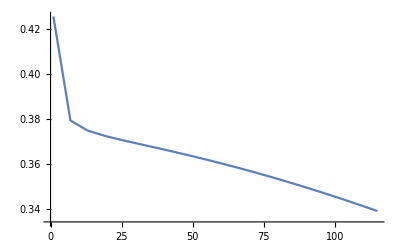

```mathematica
ListLinePlot[meanNomYieldCurve/.sol0]
```